## BeamNG Simulation data

### Importing simulations

```mathematica
ToAbsolutePath[path_,absolute_:False]:=If[absolute,path,FileNameJoin[{NotebookDirectory[],path}]];
```

```mathematica
(* Import a single simulation JSON file (via relative path). Returns an association. *)
ImportSimulation[path_,absolute_:False]:=Module[{ap,s},
s=Import[ToAbsolutePath[path,absolute], "RawJSON"];
s[["road","nodes"]]=s[["road","nodes",All,{1,2}]];
s[["records"]]=MapAt[#[[1;;2]]&,s[["records"]],{All,"pos"}];
s
]
```

```mathematica
(* Some information about the schema *)
simulation=ImportSimulation["simulation.full.json"];
simulation[["params"]]//Keys
simulation[["info"]]//Keys
simulation[["road"]]//Keys
simulation[["records"]]//First//Keys
```

{beamng_steps,delay_msec}

{id,success,start_time,computer_name,end_time}

{name,nodes}

{timer,pos,dir,vel,steering,steering_input,brake,brake_input,throttle,throttle_input,wheelspeed,vel_kmh,is_oob,oob_counter,max_oob_percentage,oob_distance}

```mathematica
(* Imports all the simulations in the ../results folder. Returns a Dataset *)
ImportSimulationFolder[path_:"../results",absolute_:False]:=Module[{ps},
ps=FileNames["simulation.full.json",ToAbsolutePath[path,absolute],2];
ImportSimulation[#,True]&/@ps
]
```

```mathematica
allSimulations=ImportSimulationFolder["1"];
```

### Convenience functions

```mathematica
RoadNodes[s_]:=s[["road","nodes",All]]
CarPositions[s_]:=s[["records",All,"pos"]]
```

### Timestamped scalar data

```mathematica
CarRecord[s_,name_]:=s[["records", All, name]]
TimestampedCarRecord[s_,name_]:=Values/@s[["records", All, {"timer",name}]]
(* Add timestamp to a list of values
	{1, 2, 3, ...} -> {{0, 1}, {0.1, 2}, {0.4, 3}, ...}
 *)
Timestamped[s_,l_]:=Transpose[{s[["records", All, "timer"]][[;;Length[l]]],l}]
```

### Visualization functions

```mathematica
(* Plots the road and the car trajectory. The black dot symbolizes the initial position of the car. *)
PlotCarTrajectory[s_]:=Show[
ListLinePlot[{
Legended[RoadNodes[s],"Road"],
Legended[CarPositions[s],"Car"]
}],
Graphics[{PointSize[Large],Point[First[CarPositions[s]]]},ImageSize->Large]
]
```

```mathematica
(* Computes the curvature at every point of a discrete curve *)
DiscreteCurvature[ps_]:=Module[{ts,ks},
ts=Map[
Function[p,
{x,y,z}=p;
VectorAngle[{0,1},y-x]-VectorAngle[{0,1},z-y]
],
Subsequences[ps,{3}]
];
ks=2Tan[#/2]&/@ts;
Join[{0},ts,{0}]
]
```

```mathematica
PlotCarDeviation[s_]:=Module[{minDistanceToRoad,velocity},
minDistanceToRoad=Timestamped[
s,
Map[
Function[p,Min[EuclideanDistance[p,#]&/@RoadNodes[s]]],
CarPositions[s]
]
];
velocity=Timestamped[s,Norm/@CarRecord[s,"vel"]];
ListLinePlot[{
Labeled[TimestampedCarRecord[s,"oob_distance"],"oob_distance"],
Labeled[minDistanceToRoad,"Distance to road center"],
Labeled[velocity,"Velocity"]
},ImageSize->Large]
]
```

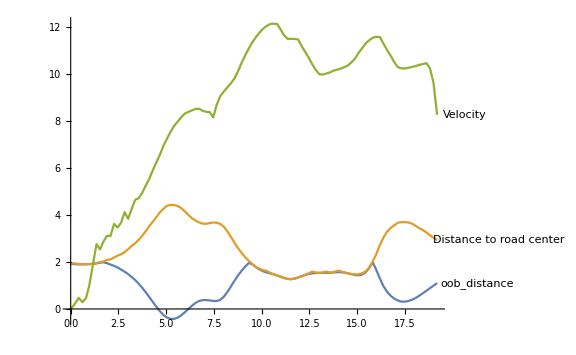

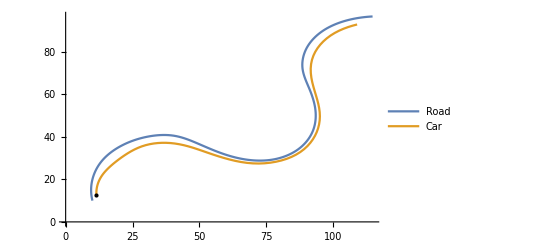

```mathematica
PlotCarDeviation[simulation]
PlotCarTrajectory[simulation]
```

```mathematica
Manipulate[
GraphicsGrid[{
{PlotCarTrajectory[allSimulations[[i]]],ListLinePlot[DiscreteCurvature[RoadNodes[allSimulations[[i]]]]]},
{PlotCarDeviation[allSimulations[[i]]]}
},ImageSize->Full],
{i,1,Length[allSimulations]}
]
```

## CSV results

### Importing

```mathematica
(* Imports a CSV point list e.g. "[(1, 2), (3, 4)]" *)
ImportCSVPointList[s_]:=Module[{ps},
ps=StringTake[s,{3,-3}];
ps=StringSplit[ps,"), ("];
ps=StringSplit[#,", "]&/@ps;
MapAt[ImportString[#,"JSON"]&,ps,{All,All}]
]

(* Imports a CSV result file. Automatically drops rows corresponding to invalid roads. *)
ImportResults[path_,absolute_:False]:=Module[{d},
d=Normal[Import[ToAbsolutePath[path,absolute], "Dataset","HeaderLines"->1]];
d=DeleteCases[d,a_/;Length[a]==0||a[["outcome"]]=="INVALID"];
Table[
r=d[[i]];
AssociateTo[r,"kappas"->If[StringLength[r[["kappas"]]]>0,ImportString[r[["kappas"]],"JSON"],{}]];
AssociateTo[r,"road"->If[StringLength[r[["road"]]]>0,ImportCSVPointList[r[["road"]]],{}]];
r,
{i,1,Length[d]}
]
]
```

```mathematica
results=ImportResults["results.csv"];
results[[1]]//Keys
```

{,description,kappas,method,outcome,road,accum_neg_oob,avg_brake,avg_brake_input,avg_oob_counter,avg_oob_distance,avg_steering,avg_steering_input,avg_throttle,avg_throttle_input,avg_vel_kmh,avg_wheelspeed,max_brake,max_brake_input,max_oob_counter,max_oob_distance,max_oob_percentage,max_steering,max_steering_input,max_throttle,max_throttle_input,max_vel_kmh,max_wheelspeed,mean_brake,mean_brake_input,mean_oob_counter,mean_oob_distance,mean_steering,mean_steering_input,mean_throttle,mean_throttle_input,mean_vel_kmh,mean_wheelspeed,min_brake,min_brake_input,min_oob_counter,min_oob_distance,min_steering,min_steering_input,min_throttle,min_throttle_input,min_vel_kmh,min_wheelspeed,parent_index,parent_min_oob_distance,parent_outcome}

-Graphics-

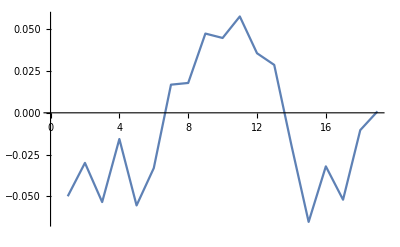

```mathematica
PlotCarTrajectory[simulation]
ListLinePlot[results[[1,"kappas"]]]
```

```mathematica
a=MapAt[Floor[10#]/10.&,RoadNodes[simulation],{All,All}];
b=MapAt[Floor[10#]/10.&,results[[1,"road"]],{All,All}];
LongestCommonSequence[b,a]//Length
```

17

## Convenience functions

```mathematica
RoadKappas[r_]:=r[["kappas"]]
```

## Full directory import

```mathematica
(* Prints basic informations about a collection of simulations *)
PrintBasicInformations[ds_,title_:"",importTime_:0]:=Print[
TableForm[
{
If[title≠"",{"","----- "<>title<>" -----"}],
If[importTime≠0,{"Import time",importTime}],
{"Count", Length[ds]},
{"Successful",Count[ds,d_/;d[["result","outcome"]]=="PASS"]},
{"Failed",Count[ds,d_/;d[["result","outcome"]]≠"PASS"]}
}
]]
```

```mathematica
ImportFolder[path_,absolute_:False]:=Module[{p,t,ss,rs,rn,ds},
p=ToAbsolutePath[path,absolute];
rn=First[FileNames["*.csv",p,1]];
t=Timing[
rs=ImportResults[rn,True];
ss=ImportSimulationFolder[p,True];
ds=Map[AssociationThread[{"simulation","result"},#]&,Transpose[{ss, rs}]];
ds=DeleteCases[ds,d_/;Length[d[["result","kappas"]]]==0];
];
PrintBasicInformations[ds,p,First[t]];
ds
]
```

```mathematica
data=ImportFolder["1"];
```

| ----- /Users/cedric/repositories/sbst-tool-competition-av/rd/1 -----
Import time | 0.512893
Count | 3
Successful | 3
Failed | 0

```mathematica
PlotCarTrajectoryWithCurvature[d_]:=Module[{plot,rcp,ccp,cplot},
plot=PlotCarTrajectory[d[["simulation"]]];
rcp=Transpose[{d[["result","road"]],d[["result","kappas"]]}];
ccp=MapAt[First@Nearest[CarPositions[d[["simulation"]]],#]&,rcp,{All,1}];
cplot=ListPlot[{
Labeled[#[[1]],SetPrecision[#[[2]],1]]&/@rcp,
First/@ccp
}];
Show[plot,cplot]
]
```

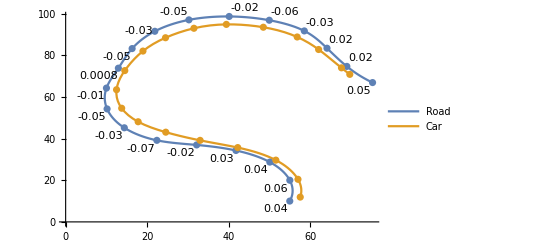

```mathematica
PlotCarTrajectoryWithCurvature[data[[3]]]
```

```mathematica
(* Returns the car records which are closest to a roat point with specified curvature. Enriches the records with these curvature values. *)
CarRecordsWithCurvature[d_]:=Module[{tp,pc,ra},
pc=Transpose[{d[["result","road"]],d[["result","kappas"]]}];
pc=MapAt[First@Nearest[CarPositions[d[["simulation"]]],#]&,pc,{All,1}];
pc=AssociationThread[{"pos","kappa"},#]&/@pc;
JoinAcross[d[["simulation","records"]],pc,Key["pos"]]
]
```

```mathematica
PlotOobToCurvature[d_,curvatureFactor_:1]:=Module[{rs,oobp,cp},
rs=CarRecordsWithCurvature[d];
oobp=Values[rs[[All,{"timer","oob_distance"}]]];
cp=Values[rs[[All,{"timer","kappa"}]]];
ListLinePlot[{
Legended[oobp,"oob_distance"],
Legended[MapAt[curvatureFactor*#&,cp,{All,2}],"Curvature * "<>ToString[curvatureFactor]]
},Filling->{1->{2}},PlotLabel->"Correlation: " <>ToString[Correlation[oobp[[All,2]],cp[[All,2]]]]]
]
```

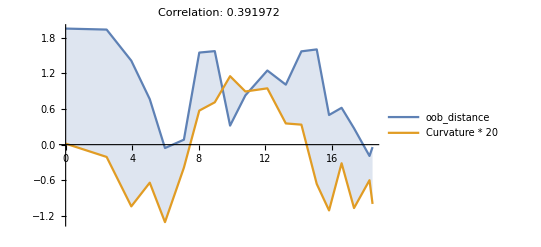

```mathematica
PlotOobToCurvature[data[[2]],20]
```

## Data consolidation

```mathematica
(* Import multiple folders at once *)
ImportFolders[paths_,absolute_:False]:=Module[{ds,t},
t=Timing[
ds=Catenate[ImportFolder[#,absolute]&/@paths];
];
PrintBasicInformations[ds,"TOTAL",First[t]];
ds
]
```

```mathematica
ImportDump[path_,absolute_:False]:=Module[{ds,t,p},
p=ToAbsolutePath[path,absolute];
t=Timing[ds=Import[ToAbsolutePath[path,absolute],"RawJSON"];];
Print[TableForm[{
{"Source", p},
{"Simulation count",Length[ds]},
{"Import time",First[t]}
}]];
ds
]
ExportDump[d_,path_,absolute_:False]:=Module[{t,p},
p=ToAbsolutePath[path,absolute];
t=Timing[Export[p,d,"RawJSON"]];
Print[TableForm[{
{"Destination", p},
{"Simulation count",Length[d]},
{"Export time",First[t]}
}]];
]
```

```mathematica
data=ImportFolders[{"1","2","3","4"}];
ExportDump[data,"1-4.dat"];
```

| ----- /Users/cedric/repositories/sbst-tool-competition-av/rd/1 -----
Import time | 0.503075
Count | 3
Successful | 3
Failed | 0

| ----- /Users/cedric/repositories/sbst-tool-competition-av/rd/2 -----
Import time | 7.04214
Count | 188
Successful | 177
Failed | 11

| ----- /Users/cedric/repositories/sbst-tool-competition-av/rd/3 -----
Import time | 6.54509
Count | 191
Successful | 176
Failed | 15

| ----- /Users/cedric/repositories/sbst-tool-competition-av/rd/4 -----
Import time | 12.4176
Count | 337
Successful | 319
Failed | 18

| ----- TOTAL -----
Import time | 26.5875
Count | 719
Successful | 675
Failed | 44

Destination | /Users/cedric/repositories/sbst-tool-competition-av/rd/1-4.dat
Simulation count | 719
Export time | 1.93509

```mathematica
data=ImportDump["1-4.dat"];
```

Source | /Users/cedric/repositories/sbst-tool-competition-av/rd/1-4.dat
Simulation count | 719
Import time | 2.01286

```mathematica
failed=Cases[data,d_/;d[["result","outcome"]]≠"PASS"];
failedDataset=ToDataset[failed];
Manipulate[
GraphicsGrid[{{
PlotCarTrajectory[failed[[i,"simulation"]]],
ListLinePlot[failedDataset[[i]]]
}},ImageSize->Large]
,{i,1,Length[failed],1}]
```

## Machine leaning experiments

### Data import

```mathematica
data=ImportDump["1-4.dat"];
```

Source | /Users/cedric/repositories/sbst-tool-competition-av/rd/1-4.dat
Simulation count | 719
Import time | 2.32625

Correlation::zerosd: The standard deviation for one or more vectors or matrix columns is zero.

General::stop: Further output of Correlation::zerosd will be suppressed during this calculation.

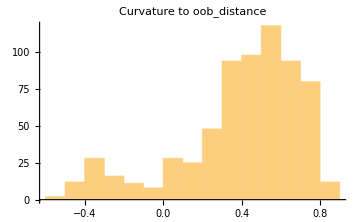
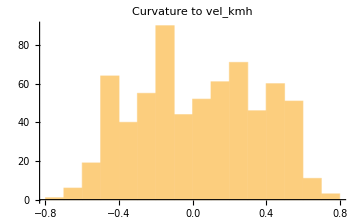
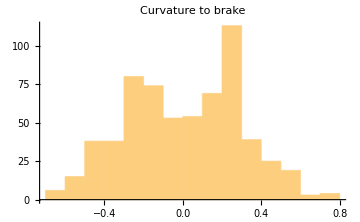

```mathematica
Table[
Histogram[
Correlation[#[[All,metric]],#[[All,"kappa"]]]&/@
(CarRecordsWithCurvature/@Cases[data,d_/;d[["result","outcome"]]=="PASS"]),
PlotLabel->"Curvature to "<>metric,ImageSize->Medium],
{metric,{"oob_distance","vel_kmh","brake"}}
]//Row
```

```mathematica
(* Creates a dataset, which is a list whose items are of the form
  {N kappa values} -> {N oob_distance values}
   WARNING: THIS MAY BE THE OPPOSITE OF WHAT YOU NEED. 
Use Reverse[dataset, {2}] to create the serverse set.
 *)
ToDataset[ds_,shuffle_:False]:=Map[
Function[d,
r=CarRecordsWithCurvature[d];
r[[All,"kappa"]]->Abs[r[[All,"oob_distance"]]]
],
If[shuffle,RandomSample,Identity][ds]
];
```

```mathematica
(* Splits a list into a training set (trainingPercentage_ % of the whose set) and a validation set *)
SplitDataset[l_,trainingPercentage_:0.8]:=Module[{i},
i=Floor[Length[l]*trainingPercentage]; 
{l[[;;i]],l[[i+1;;]]}
]
```

```mathematica
(* Plots a histogram representing the accuracy if a predictor against a validation set. *)
PlotAccuracy[predictor_,validationSet_]:=Histogram[EuclideanDistance[predictor[#[[1]]],#[[2]]]&/@validationSet]
```

### Dimension reduction

```mathematica
passDataset=ToDataset[Cases[data,d_/;d[["result","outcome"]]=="PASS"]];
failDataset=ToDataset[Cases[data,d_/;d[["result","outcome"]]!="PASS"]];
```

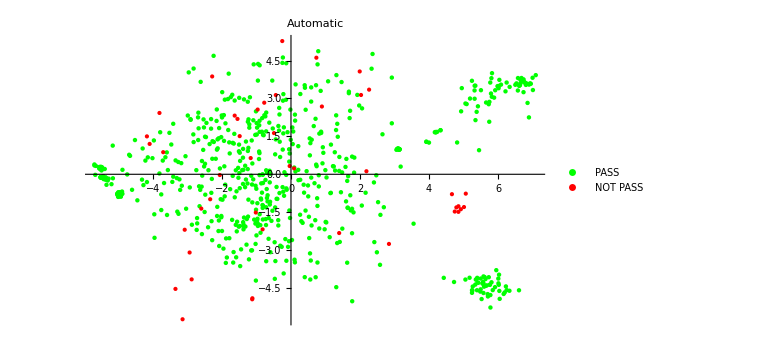
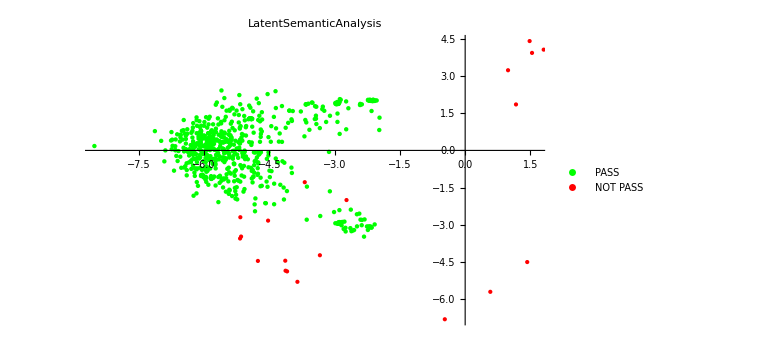
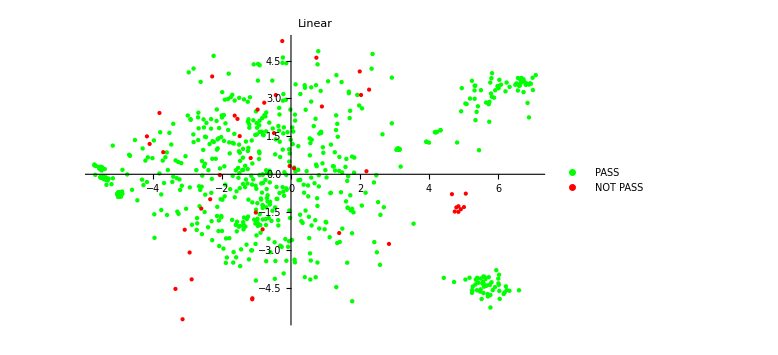
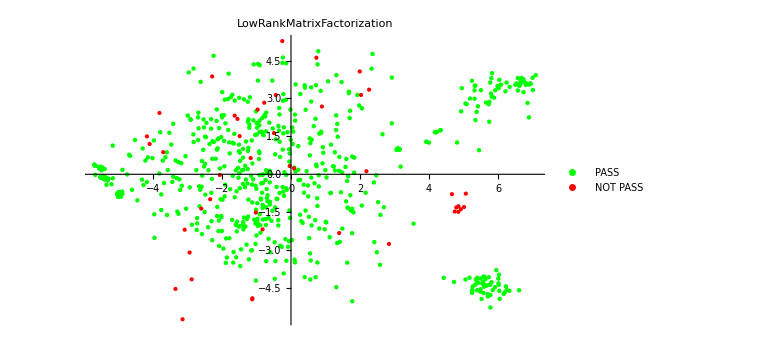
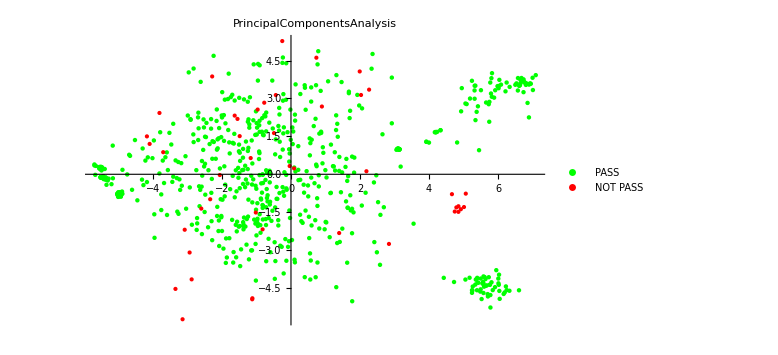
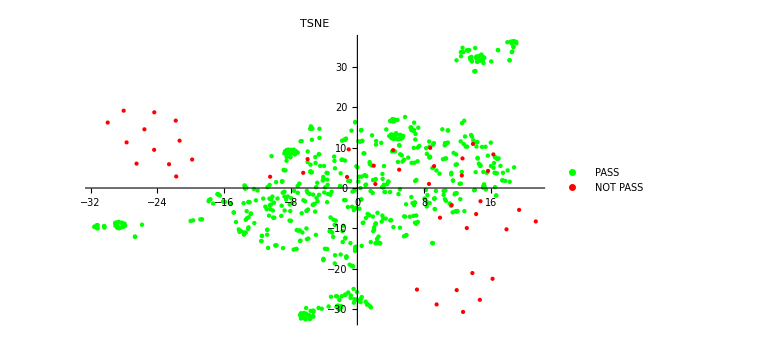
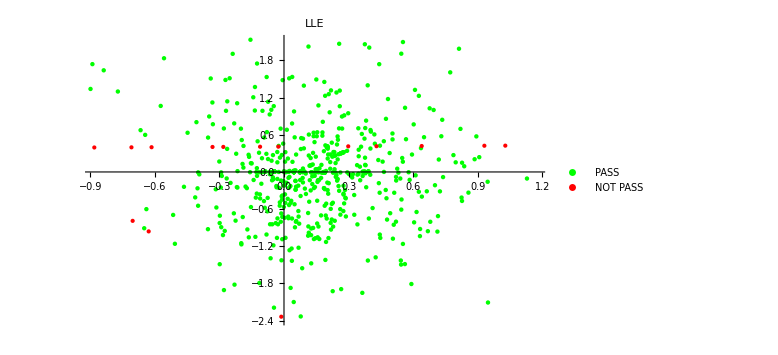
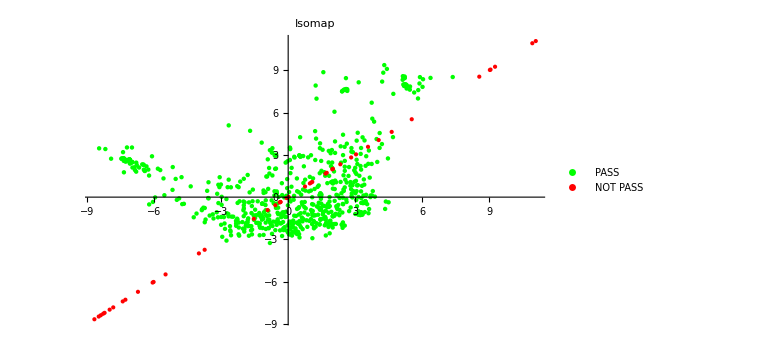

```mathematica
methods={Automatic,"LatentSemanticAnalysis","Linear","LowRankMatrixFactorization","PrincipalComponentsAnalysis","TSNE","LLE","Isomap"};
Table[
ListPlot[{
Legended[DimensionReduce[passDataset,Method->m],"PASS"],
Legended[DimensionReduce[failDataset,Method->m],"NOT PASS"]
},PlotLabel->m,ImageSize->Large,PlotStyle->{Green,{Red,PointSize[Large]}}],
{m,methods}
]//Column
```

### Predicting |min_oob_distance|

```mathematica
dataset=#[["result","kappas"]]->Abs[#[["result","min_oob_distance"]]]&/@data;
{trainingDataset,validationDataset}=SplitDataset[RandomSample[dataset],0.8];
```

```mathematica
methods={"DecisionTree","GradientBoostedTrees","LinearRegression","NearestNeighbors","NeuralNetwork","RandomForest","GaussianProcess"};
predictors=AssociationMap[Predict[trainingDataset,Method->#]&,methods];
```

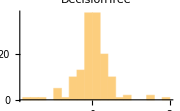
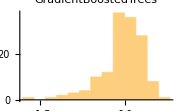
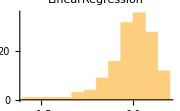
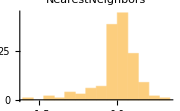
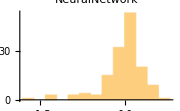
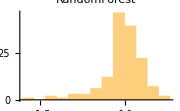
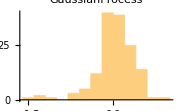

```mathematica
KeyValueMap[
Function[
{m,p},
Histogram[p[#[[1]]]-#[[2]]&/@validationDataset,PlotLabel->m,ImageSize->Small]
],
predictors
]//Row
```

### Predicting the car trajectory

Here, we are predicting all 19 oob_distance values separately

```mathematica
data//First//CarRecordsWithCurvature//Length
```

19

```mathematica
{trainingDataset,validationDataset}=SplitDataset[ToDataset[data,True],0.9];
```

```mathematica
predictors=ParallelTable[
Predict[#[[1]]->#[[2,i]]&/@trainingDataset,Method->"DecisionTree",TrainingProgressReporting->None],
{i,1,19}
];
```

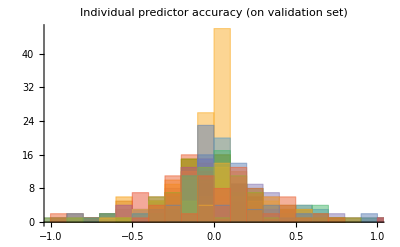

```mathematica
Histogram[Table[
predictors[[i]][#[[1]]]-#[[2,i]]&/@validationDataset,
{i,1,19}
],PlotLabel->"Individual predictor accuracy (on validation set)"]
```

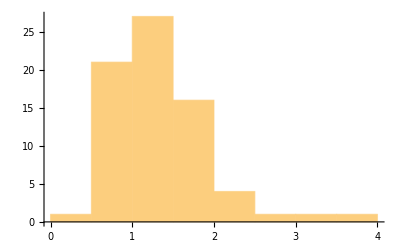

```mathematica
PlotAccuracy[Function[ks,Table[p[ks],{p,predictors}]],validationDataset]
```

```mathematica
Manipulate[
d=Table[p[validationDataset[[j,1]]],{p,predictors}];
ListLinePlot[{
Legended[validationDataset[[j,2]],"Real oob_distance"],
Legended[d,"Predicted oob_distance"]
},ImageSize->Large,Filling->{2->{1}}],
{j,1,Length[validationDataset],1}
]
```

### Predicting the curvature

```mathematica
{trainingDataset,validationDataset}=SplitDataset[Reverse[ToDataset[data,True],{2}],0.9];
```

The predictors are expected to predict a curvature value given the oob_distance’s values of the car

```mathematica
predictors=ParallelTable[
Predict[#[[1]]->#[[2,i]]&/@trainingDataset,Method->"DecisionTree",TrainingProgressReporting->None],
{i,1,19}
];
```

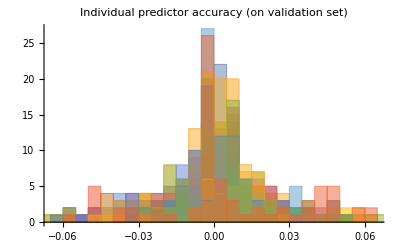

```mathematica
Histogram[Table[
predictors[[i]][#[[1]]]-#[[2,i]]&/@validationDataset,
{i,1,19}
],PlotLabel->"Individual predictor accuracy (on validation set)"]
```

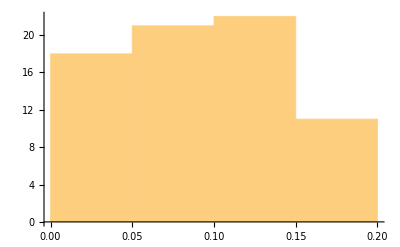

```mathematica
PlotAccuracy[Function[ks,Table[p[ks],{p,predictors}]],validationDataset]
```

```mathematica
Manipulate[
d=Table[p[validationDataset[[j,2]]],{p,predictors}];
ListLinePlot[{
Legended[validationDataset[[j,1]],"Real curvature"],
Legended[d,"Predicted curvature"]
},ImageSize->Large,Filling->{2->{1}}],
{j,1,Length[validationDataset],1}
]
```

### Neural networks

```mathematica
network=NetChain[{
LinearLayer[]
}]
```